```mathematica
y1=Import["~/desertbus/graph/year1.json"];
y2=Import["~/desertbus/graph/year2.json"];
y3=Import["~/desertbus/graph/year3.json"];
y4=Import["~/desertbus/graph/year4.json"];
y5=Import["~/desertbus/graph/year5.json"];
y6=Import["~/desertbus/graph/year6.json"];
y7=Import["~/desertbus/graph/year7.json"];
y8=Import["~/desertbus/graph/year8.json"];
y9=Import["~/desertbus/graph/year9.json"];
```

```mathematica
f1[year_,month_,day_,hour_,minute_,money_]:={AbsoluteTime[{year,month,day,hour,minute,0}],money}
f2[year_,month_,day_,hour_,minute_,money_,last_,start_]:=
{AbsoluteTime[{year,month,day,hour,minute,0}],money}
norm[list_]:={#1-list[[1,1]],#2}&@@#&/@list
```

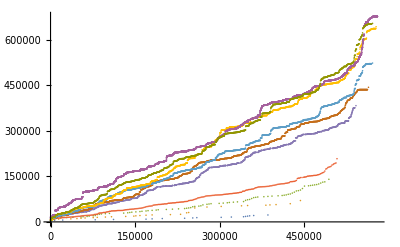

~/desertbus/graph/graph1.pdf

```mathematica
ListPlot[norm/@Join[
f1@@#&/@#&/@{y1,y2,y3,y4,y5},
f2@@#&/@#&/@{y6,y7,y8,y9},
{#[[1]],#[[2]]*1.25}&@*f2@@#&/@#&/@{y7}
],ImageSize->Full]
Export["~/desertbus/graph/graph1.pdf",%]
```

{{2007,22805},{2008,70423.8},{2009,140450.},{2010,208250},{2011,383125.},{2012,443630.},{2013,523520},{2014,643243.},{2015,677158}}

-1.76413×10^8+87897.1 x+30859. Sin[x]+16572.8 Sin[2 x]

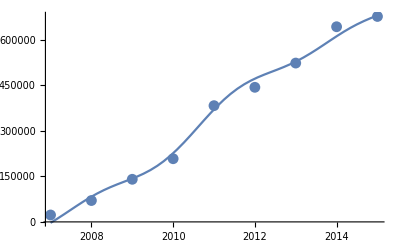

746965.

```mathematica
Join[
f1@@#&/@#&/@{y1,y2,y3,y4,y5},
f2@@#&/@#&/@{y6,y7,y8,y9}
];
{Range[2007,2015],#[[-1,2]]&/@%}ᵀ
fit=Fit[%,{1,x,Sin[x],Sin[2x]},x]
Plot[%,{x,2007,2015}];
ListPlot[%%%];
Show[%,%%]
fit/.{x->2016}//AccountingForm
```

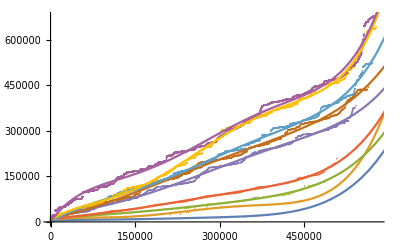

~/desertbus/graph/graph2.pdf

```mathematica
norm/@Join[
f1@@#&/@#&/@{y1,y2,y3,y4,y5},
f2@@#&/@#&/@{y6,y7,y8,y9}];
fits=Fit[#,{1,x,x^2,x^3,x^4,x^5},x]&/@%;
ListPlot[%%];
Plot[%%,{x,0,%%%[[-2,-1,-1]]}];
Show[%%,%,ImageSize->Full]
Export["~/desertbus/graph/graph2.pdf",%]
```

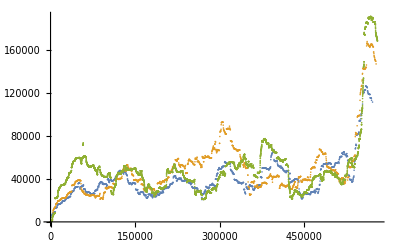

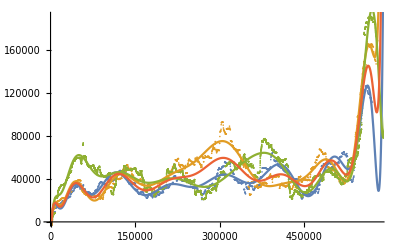

~/desertbus/graph/graph3.pdf

```mathematica
f22[year_,month_,day_,hour_,minute_,money_,last_,start_]:=
{AbsoluteTime[{year,month,day,hour,minute,0}],If[last<100000,last,0]};
norm@(f22@@#&/@#)&/@{y7,y8,y9};
MovingMap[Total,#,{{50000}},0]&/@%;
ListPlot[%,ImageSize->Full, PlotRange->All]
Fit[#,Table[x^c,{c,0,17}],x]&/@%%; 
Append[%,Mean[%[[1;;2]]]];
Plot[%,{x,0,600000}, PlotRange->All];
Show[%%%%,%,ImageSize->Full]
Export["~/desertbus/graph/graph3.pdf",%]
```

```mathematica
Join[
f1@@#&/@#&/@{y1,y2,y3,y4,y5},
f2@@#&/@#&/@{y6,y7,y8}
];
%[[-1,-1,2]]*1.25
```

804053.

```mathematica
fits=Fit[norm@({#[[1]],#[[2]]*1.25}&@*f2@@#&/@y7),{1,x,x^2,x^3,x^4,x^5},x]
Solve[%==506641.00+(3000000-2942087.15),x,Reals]
AbsoluteTime[y9[[1,1;;5]]]+x/.%[[1]]
DateList[%]
```

-2834.84+1.60232 x-0.0000108084 x^2+5.67771×10^-11 x^3-1.22964×10^-16 x^4+9.52525×10^-23 x^5

{{x→538311.}}

3.65702×10^9

{2015,11,20,15,31,50.72}